Calculando órbita: e=0.5, l=11., M=3/14

μ = 0.0194805, A = 0.902597, k.b2 = 0.0431655

Perihelio: r = 7.33333

Afelio: r = 22.

Calculando órbita: e=0.5, l=7.5, M=3/14

μ = 0.0285714, A = 0.857143, k.b2 = 0.0666667

Perihelio: r = 5.

Afelio: r = 15.

Calculando órbita: e=0.5, l=3., M=3/14

μ = 0.0714286, A = 0.642857, k.b2 = 0.222222

Perihelio: r = 2.

Afelio: r = 6.

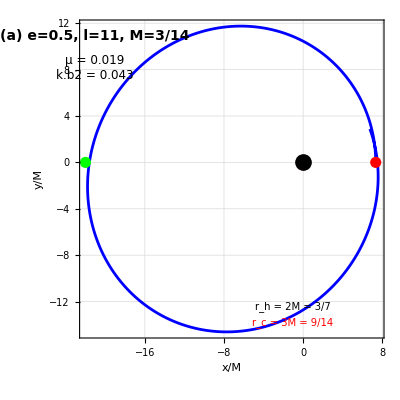
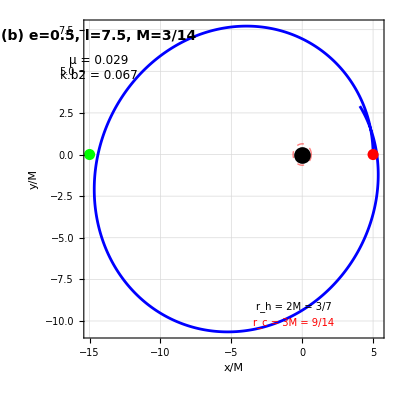
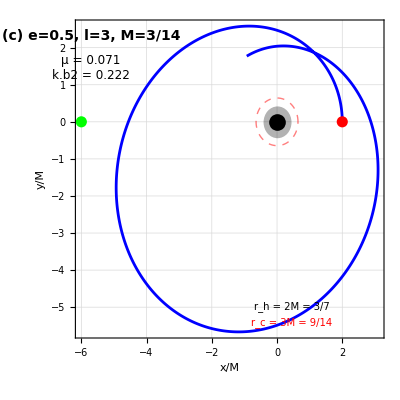

==============================================================

PRECESIÓN DEL PERIHELIO (aproximación post-newtoniana):

Δφ = 6πM/l por revolución

==============================================================

(a) e=0.5, l=11, M=3/14: Δφ = 0.3672 rad = 21.04° por revolución

(b) e=0.5, l=7.5, M=3/14: Δφ = 0.5386 rad = 30.86° por revolución

(c) e=0.5, l=3, M=3/14: Δφ = 1.3464 rad = 77.14° por revolución

¡Gráficos generados exitosamente!

```mathematica
(*Código para graficar órbitas relativistas en Schwarzschild según Chandrasekhar,The Mathematical Theory of Black Holes Figura 7a (a),(b),(c)-Órbitas de primera clase (E^2<1)*)ClearAll["Global`*"]

(* =======================================================================*)
(*PARÁMETROS DE LAS ÓRBITAS*)
(* =======================================================================*)

(*Valores de la figura 7a (a),(b),(c)*)
paramSets={{"(a) e=0.5, l=11, M=3/14",0.5,11.0,3/14},{"(b) e=0.5, l=7.5, M=3/14",0.5,7.5,3/14},{"(c) e=0.5, l=3, M=3/14",0.5,3.0,3/14}};

(* =======================================================================*)
(*FUNCIONES AUXILIARES*)
(* =======================================================================*)

(*Función para calcular μ=M/l*)
CalcMu[M_,l_]:=M/l;

(*Función para calcular A=1-6μ+2μe*)
CalcA[mu_,e_]:=1-6*mu+2*mu*e;

(*Función para calcular k.b2=4μe/A*)
Calck2[mu_,e_,A_]:=If[A!=0,4*mu*e/A,1.0];

(*Función para calcular φ(χ) usando la ecuación (132):φ=2/√A*F(π/2-χ/2,k) donde F es la integral elíptica incompleta de primera especie Usamos EllipticF[ψ,k.b2] en Mathematica*)
PhiFromChi[chi_,A_,k2_]:=Module[{sqrtA,psi},If[A<=0,Return[Indeterminate]];
sqrtA=Sqrt[A];
psi=Pi/2-chi/2;
2*EllipticF[psi,k2]/sqrtA];

(*Función para calcular la órbita completa r(φ) Devuelve lista de {r,φ} para un conjunto de parámetros*)
CalcOrbit[e_,l_,M_,nPoints_:500]:=Module[{mu,A,k2,chiVals,phiVals,rVals,orbitData},mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
(*Verificar parámetros válidos*)If[A<=0||k2<0,Print["Parámetros inválidos: A = ",A,", k.b2 = ",k2];
Return[{},Module];];
Print["Calculando órbita: e=",e,", l=",l,", M=",M];
Print["  μ = ",mu,", A = ",A,", k.b2 = ",k2];
(*Rango de χ de 0 a 2π*)chiVals=Range[0,2*Pi,2*Pi/(nPoints-1)];
(*Calcular φ para cada χ*)phiVals=PhiFromChi[#,A,k2]&/@chiVals;
(*Calcular r=1/u,con u=(1+e cosχ)/l*)rVals=l/(1+e*Cos[chiVals]);
(*Ajustar φ para empezar en 0*)phiMin=Min[phiVals];
phiValsAdj=phiVals-phiMin;
(*Asegurar que φ sea monótono creciente*)If[AnyTrue[Differences[phiValsAdj],#<0&],phiValsAdj=2*Pi*UnitStep[phiValsAdj]+phiValsAdj;];
(*Crear lista de {x,y} coordenadas cartesianas*)xVals=rVals*Cos[phiValsAdj];
yVals=rVals*Sin[phiValsAdj];
orbitData=Transpose[{xVals,yVals}];
Print["  Perihelio: r = ",l/(1+e)];
Print["  Afelio: r = ",If[e<1,l/(1-e),"∞"]];
orbitData];

(* =======================================================================*)
(*CREACIÓN DE GRÁFICOS*)
(* =======================================================================*)

(*Crear gráficos individuales*)
orbitPlots=Table[Module[{label,e,l,M,orbitData,rHorizon,rCritical,perihelio,afelio,mu,A,k2,rPeri,rAp,plot},{label,e,l,M}=paramSet;
mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
orbitData=CalcOrbit[e,l,M,1000];
If[Length[orbitData]==0,Return[Graphics[{Text["Parámetros inválidos",{0,0}]}]]];
(*Radios importantes*)rHorizon=2*M;
rCritical=3*M;
rPeri=l/(1+e);
rAp=If[e<1,l/(1-e),100*M];(*Si e>=1,usar valor grande*)(*Gráfico principal*)plot=Show[(*Órbita*)ListLinePlot[orbitData,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All,AspectRatio->1],(*Horizonte de eventos*)Graphics[{Black,Opacity[0.3],Disk[{0,0},rHorizon]}],(*Órbita circular crítica (r=3M)*)Graphics[{Red,Dashed,Opacity[0.5],Circle[{0,0},rCritical]}],(*Centro (agujero negro)*)Graphics[{Black,PointSize[0.03],Point[{0,0}]}],(*Perihelio*)Graphics[{Red,PointSize[0.02],Point[{rPeri*Cos[0],rPeri*Sin[0]}]}],(*Afelio (si es órbita ligada)*)If[e<1,Graphics[{Green,PointSize[0.02],Point[{-rAp,0}]}],Graphics[]],(*Etiquetas*)Graphics[{Text[Style[label,14,Bold],Scaled[{0.05,0.95}]],Text[Style[StringForm["μ = ``\nk.b2 = ``",NumberForm[mu,{4,3}],NumberForm[k2,{4,3}]],12],Scaled[{0.05,0.85}]],Text[Style[StringForm["r_h = 2M = ``",NumberForm[rHorizon,{4,2}]],10],Scaled[{0.7,0.1}]],Text[Style[StringForm["r_c = 3M = ``",NumberForm[rCritical,{4,2}]],10,Red],Scaled[{0.7,0.05}]]}],(*Configuración del gráfico*)Frame->True,FrameLabel->{"x/M","y/M"},FrameStyle->Thickness[0.002],PlotRange->All,ImageSize->400,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]]];
plot],{paramSet,paramSets}];

(* =======================================================================*)
(*MOSTRAR GRÁFICOS COMBINADOS*)
(* =======================================================================*)

(*Mostrar los tres gráficos en una fila*)
Row[orbitPlots,Spacer[10]]

(* =======================================================================*)
(*CÁLCULO DE PRECESIÓN DEL PERIHELIO*)
(* =======================================================================*)

Print["\n=============================================================="];
Print["PRECESIÓN DEL PERIHELIO (aproximación post-newtoniana):"];
Print["Δφ = 6πM/l por revolución"];
Print["=============================================================="];

Do[{label,e,l,M}=paramSet;
deltaPhi=6*Pi*M/l;
deltaPhiDeg=deltaPhi*180/Pi;
Print[label,": Δφ = ",NumberForm[deltaPhi,{5,4}]," rad = ",NumberForm[deltaPhiDeg,{5,2}],"° por revolución"],{paramSet,paramSets}];

(* =======================================================================*)
(*ANIMACIÓN OPCIONAL:Evolución de la órbita en función de χ*)
(* =======================================================================*)

(*Para crear una animación de cómo evoluciona la órbita,descomentar las siguientes líneas:*)

(*Print["\nCreando animación de la órbita (c)..."];
{e,l,M}={0.5,3.0,3/14};
mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
animation=Animate[Show[ParametricPlot[{l/(1+e*Cos[chi])*Cos[PhiFromChi[chi,A,k2]],l/(1+e*Cos[chi])*Sin[PhiFromChi[chi,A,k2]]},{chi,0,chiMax},PlotStyle->{Blue,Thickness[0.005]},PlotRange->{{-10,10},{-10,10}}],Graphics[{{Black,Opacity[0.3],Disk[{0,0},2*M]},{Red,Dashed,Circle[{0,0},3*M]},{Black,PointSize[0.03],Point[{0,0}]},Text[Style[StringForm["χ = ``",NumberForm[chiMax,{4,2}]],14],{8,8}]}],Frame->True,AspectRatio->1,ImageSize->400],{chiMax,0.1,2*Pi,0.1},AnimationRunning->False];*)

(*Exportar gráficos a PDF*)
(*Export["OrbitasChandrasekhar.pdf",Row[orbitPlots,Spacer[10]]];*)

Print["\n¡Gráficos generados exitosamente!"];
```

Calculando órbita: e=0.5, l=11., M=3/14, revoluciones=3

μ = 0.01948, A = 0.9026, k.b2 = 0.04317

Ángulo por revolución: Δφ = 6.68668 rad

Precesión por revolución: 0.403493 rad = 23.12°

Calculando órbita: e=0.5, l=7.5, M=3/14, revoluciones=3

μ = 0.02857, A = 0.8571, k.b2 = 0.06667

Ángulo por revolución: Δφ = 6.90417 rad

Precesión por revolución: 0.620989 rad = 35.58°

Calculando órbita: e=0.5, l=3., M=3/14, revoluciones=5

μ = 0.07143, A = 0.6429, k.b2 = 0.2222

Ángulo por revolución: Δφ = 8.33643 rad

Precesión por revolución: 2.05325 rad = 117.6°

GRÁFICOS DE ÓRBITAS CON MÚLTIPLES REVOLUCIONES

==============================================

StringForm::sfr: Item 4 requested in "Precesión: {`4f`}°/rev" out of range; 1 items available.

General::stop: Further output of StringForm::sfr will be suppressed during this calculation.

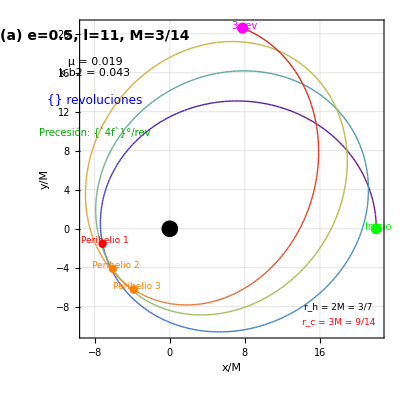
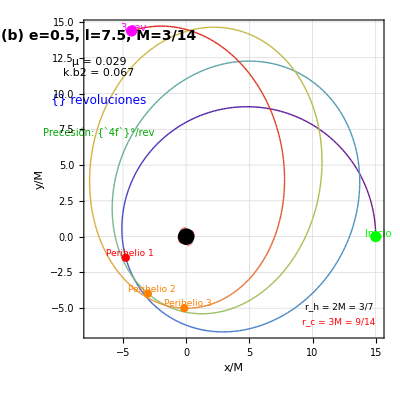
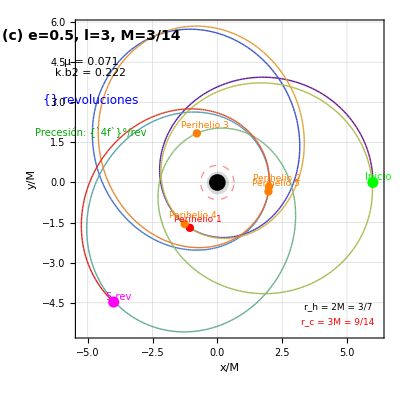

CREANDO ANIMACIÓN DETALLADA PARA ÓRBITA (c)...

Calculando órbita: e=0.5, l=3., M=3/14, revoluciones=5

μ = 0.07143, A = 0.6429, k.b2 = 0.2222

Ángulo por revolución: Δφ = 8.33643 rad

Precesión por revolución: 2.05325 rad = 117.6°

¡Gráficos y animación generados exitosamente!

"\\n

```mathematica
(*Código para graficar órbitas relativistas en Schwarzschild con múltiples revoluciones para mostrar precesión del perihelio*)ClearAll["Global`*"]

(* =======================================================================*)
(*PARÁMETROS DE LAS ÓRBITAS*)
(* =======================================================================*)

(*Valores de la figura 7a (a),(b),(c) con número de revoluciones*)
paramSets={{"(a) e=0.5, l=11, M=3/14",0.5,11.0,3/14,3},{"(b) e=0.5, l=7.5, M=3/14",0.5,7.5,3/14,3},{"(c) e=0.5, l=3, M=3/14",0.5,3.0,3/14,5}  (*Más revoluciones para órbita más cercana*)};

(* =======================================================================*)
(*FUNCIONES AUXILIARES*)
(* =======================================================================*)

(*Función para calcular μ=M/l*)
CalcMu[M_,l_]:=M/l;

(*Función para calcular A=1-6μ+2μe*)
CalcA[mu_,e_]:=1-6*mu+2*mu*e;

(*Función para calcular k.b2=4μe/A*)
Calck2[mu_,e_,A_]:=If[A!=0,4*mu*e/A,1.0];

(*Función para calcular φ(χ) usando la ecuación (132):φ=2/√A*F(π/2-χ/2,k)*)
PhiFromChi[chi_,A_,k2_]:=Module[{sqrtA,psi},If[A<=0,Return[Indeterminate]];
sqrtA=Sqrt[A];
psi=Pi/2-chi/2;
2*EllipticF[psi,k2]/sqrtA];

(*Función para calcular la órbita completa para múltiples revoluciones Devuelve lista de {x,y} para n revoluciones*)
CalcOrbitMultiple[e_,l_,M_,nRevolutions_:3,nPointsPerRev_:200]:=Module[{mu,A,k2,chiVals,phiVals,rVals,allChi,allPhi,allR,allX,allY,phiPerRev,precession},mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
(*Verificar parámetros válidos*)If[A<=0||k2<0,Print["Parámetros inválidos: A = ",A,", k.b2 = ",k2];
Return[{},Module];];
Print["Calculando órbita: e=",e,", l=",l,", M=",M,", revoluciones=",nRevolutions];
Print["  μ = ",NumberForm[mu,4],", A = ",NumberForm[A,4],", k.b2 = ",NumberForm[k2,4]];
(*Una revolución:χ de π (afelio) a-π (siguiente afelio)*)chiValsOneRev=Range[Pi,-Pi,-2*Pi/(nPointsPerRev-1)];
phiValsOneRev=PhiFromChi[#,A,k2]&/@chiValsOneRev;
(*Ángulo φ por revolución*)phiPerRev=phiValsOneRev[[-1]]-phiValsOneRev[[1]];
Print["  Ángulo por revolución: Δφ = ",NumberForm[phiPerRev,6]," rad"];
(*Precesión por revolución*)precession=phiPerRev-2*Pi;
Print["  Precesión por revolución: ",NumberForm[precession,6]," rad = ",NumberForm[precession*180/Pi,4],"°"];
(*Generar múltiples revoluciones*)allChi={};
allPhi={};
For[rev=0,rev<nRevolutions,rev++,chiOffset=rev*2*Pi;
phiOffset=rev*phiPerRev;
chiValsAdj=chiValsOneRev-chiOffset;
phiValsAdj=phiValsOneRev-phiValsOneRev[[1]]+phiOffset;
allChi=Join[allChi,chiValsAdj];
allPhi=Join[allPhi,phiValsAdj];];
(*Calcular r=l/(1+e cosχ)*)allR=l/(1+e*Cos[allChi]);
(*Convertir a coordenadas cartesianas*)allX=allR*Cos[allPhi];
allY=allR*Sin[allPhi];
(*Ajustar para que φ empiece en 0*)phiMin=Min[allPhi];
allPhiAdj=allPhi-phiMin;
allX=allR*Cos[allPhiAdj];
allY=allR*Sin[allPhiAdj];
Transpose[{allX,allY}]];

(* =======================================================================*)
(*CREACIÓN DE GRÁFICOS CON MÚLTIPLES REVOLUCIONES*)
(* =======================================================================*)

(*Crear gráficos individuales con múltiples revoluciones*)
orbitPlotsMultiple=Table[Module[{label,e,l,M,nRevs,orbitData,rHorizon,rCritical,perihelio,afelio,mu,A,k2,rPeri,rAp,plot,colorFunction,colors,phiPerRev,precession},{label,e,l,M,nRevs}=paramSet;
mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
orbitData=CalcOrbitMultiple[e,l,M,nRevs,300];
If[Length[orbitData]==0,Return[Graphics[{Text["Parámetros inválidos",{0,0}]}]]];
(*Calcular φ por revolución para etiquetas*)phiPerRev=2*Pi+6*Pi*M/l;(*Aproximación post-newtoniana*)precession=phiPerRev-2*Pi;
(*Radios importantes*)rHorizon=2*M;
rCritical=3*M;
rPeri=l/(1+e);
rAp=If[e<1,l/(1-e),100*M];
(*Función de color para mostrar progresión temporal*)nPoints=Length[orbitData];
colorFunction=ColorData["Rainbow"];
colors=Table[colorFunction[i/nPoints],{i,0,nPoints-1}];
(*Gráfico principal con color progresivo*)plot=Show[(*Órbita con color que muestra evolución*)Graphics[Table[{colors[[i]],Line[{orbitData[[i]],orbitData[[i+1]]}]},{i,1,Length[orbitData]-1}]],(*Horizonte de eventos*)Graphics[{Black,Opacity[0.15],Disk[{0,0},rHorizon]}],(*Órbita circular crítica (r=3M)*)Graphics[{Red,Dashed,Opacity[0.5],Thickness[0.002],Circle[{0,0},rCritical]}],(*Centro (agujero negro)*)Graphics[{Black,PointSize[0.03],Point[{0,0}]}],(*Marcar inicio y fin*)Graphics[{{Green,PointSize[0.02],Point[orbitData[[1]]],Text[Style["Inicio",10,Green],orbitData[[1]]+{0.2,0.2}]},{Magenta,PointSize[0.02],Point[orbitData[[-1]]],Text[Style[ToString[nRevs]<>" rev",10,Magenta],orbitData[[-1]]+{0.2,0.2}]}}],(*Marcar perihelios sucesivos*)Graphics[Table[Module[{periPoints,periIdx},(*Encontrar perihelio en cada revolución*)pointsPerRev=Length[orbitData]/nRevs;
startIdx=Round[(rev-1)*pointsPerRev]+1;
endIdx=Round[rev*pointsPerRev];
If[endIdx>Length[orbitData],endIdx=Length[orbitData]];
segment=orbitData[[startIdx;;endIdx]];
distances=Norm/@segment;
periIdx=Position[distances,Min[distances]][[1,1]];
periPoint=segment[[periIdx]];
{If[rev==1,Red,Orange],PointSize[0.015],Point[periPoint],If[rev==1,Text[Style["Perihelio 1",9,Red],periPoint+{0.3,0.3}],Text[Style["Perihelio "<>ToString[rev],9,Orange],periPoint+{0.3,0.3}]]}],{rev,1,nRevs}]],(*Etiquetas y texto informativo*)Graphics[{Text[Style[label,14,Bold],Scaled[{0.05,0.95}]],Text[Style[StringForm["μ = ``\nk.b2 = ``",NumberForm[mu,{4,3}],NumberForm[k2,{4,3}]],11],Scaled[{0.05,0.85}]],Text[Style[StringForm["{} revoluciones",nRevs],12,Blue],Scaled[{0.05,0.75}]],Text[Style[StringForm["Precesión: {`4f`}°/rev",precession*180/Pi],10,Darker[Green]],Scaled[{0.05,0.65}]],Text[Style[StringForm["r_h = 2M = ``",NumberForm[rHorizon,{4,2}]],9],Scaled[{0.85,0.1}]],Text[Style[StringForm["r_c = 3M = ``",NumberForm[rCritical,{4,2}]],9,Red],Scaled[{0.85,0.05}]]}],(*Configuración del gráfico*)Frame->True,FrameLabel->{"x/M","y/M"},FrameStyle->Thickness[0.002],PlotRange->All,AspectRatio->1,ImageSize->400,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.2]]];
plot],{paramSet,paramSets}];

(* =======================================================================*)
(*MOSTRAR GRÁFICOS COMBINADOS*)
(* =======================================================================*)

(*Mostrar los tres gráficos en una fila*)
Print["GRÁFICOS DE ÓRBITAS CON MÚLTIPLES REVOLUCIONES"];
Print["=============================================="];
Row[orbitPlotsMultiple,Spacer[10]]

(* =======================================================================*)
(*ANIMACIÓN DETALLADA PARA UNA ÓRBITA ESPECÍFICA*)
(* =======================================================================*)

(*Seleccionar una órbita para animación detallada*)
Print["\nCREANDO ANIMACIÓN DETALLADA PARA ÓRBITA (c)..."];

{e,l,M,nRevs}={0.5,3.0,3/14,5};
mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];

(*Calcular datos para animación*)
orbitDataAnim=CalcOrbitMultiple[e,l,M,nRevs,100];
nPointsAnim=Length[orbitDataAnim];

(*Crear animación paso a paso*)
animation=Animate[Show[(*Trazo completo en gris claro de fondo*)Graphics[{LightGray,Opacity[0.3],Line[orbitDataAnim]},PlotRange->{{-8,8},{-8,8}}],(*Trazo animado en color*)Graphics[{ColorData["Rainbow"][t],Thickness[0.005],Line[Take[orbitDataAnim,Floor[t*nPointsAnim]]]}],(*Punto móvil*)Graphics[{Red,PointSize[0.03],Point[orbitDataAnim[[Floor[t*nPointsAnim]]]]}],(*Elementos fijos*)Graphics[{{Black,Opacity[0.2],Disk[{0,0},2*M]},{Red,Dashed,Circle[{0,0},3*M]},{Black,PointSize[0.04],Point[{0,0}]},Text[Style[StringForm["Revolución {`1f`}/{}",t*nPointsAnim/(nPointsAnim/nRevs),nRevs],14,Bold],{6,7}]}],Frame->True,FrameLabel->{"x/M","y/M"},AspectRatio->1,ImageSize->500,PlotRange->{{-8,8},{-8,8}}],{t,0,1,0.01},AnimationRunning->False,AnimationRepetitions->1];

(*Mostrar animación*)
animation

(* =======================================================================*)
(*EXPORTAR GRÁFICOS*)
(* =======================================================================*)

(*Exportar a PDF*)
(*Export["OrbitasMultiplesRevoluciones.pdf",Grid[{{orbitPlotsMultiple[[1]],orbitPlotsMultiple[[2]],orbitPlotsMultiple[[3]]}}]];*)

(*Exportar animación a GIF*)
(*Export["OrbitaAnimacion.gif",animation,"AnimationRepetitions"->Infinity];*)

Print["\n¡Gráficos y animación generados exitosamente!"];
```

Ahora si?

======================================================================

CREANDO ANIMACIONES DETALLADAS PARA LAS TRES ÓRBITAS

======================================================================

------------------------------------------------------------

Creando animación para: (a) e=0.5, l=11, M=3/14

μ = 0.01948, k.b2 = 0.04317

Perihelio: r = 7.333

Afelio: r = 22.

Precesión: 23.12°/rev

Puntos totales: 800

------------------------------------------------------------

Creando animación para: (b) e=0.5, l=7.5, M=3/14

μ = 0.02857, k.b2 = 0.06667

Perihelio: r = 5.

Afelio: r = 15.

Precesión: 35.58°/rev

Puntos totales: 1200

------------------------------------------------------------

Creando animación para: (c) e=0.5, l=3, M=3/14

μ = 0.07143, k.b2 = 0.2222

Perihelio: r = 2.

Afelio: r = 6.

Precesión: 117.6°/rev

Puntos totales: 2000

======================================================================

MOSTRANDO ANIMACIONES EN CUADRÍCULA

(Cada animación tiene controles independientes de reproducción)

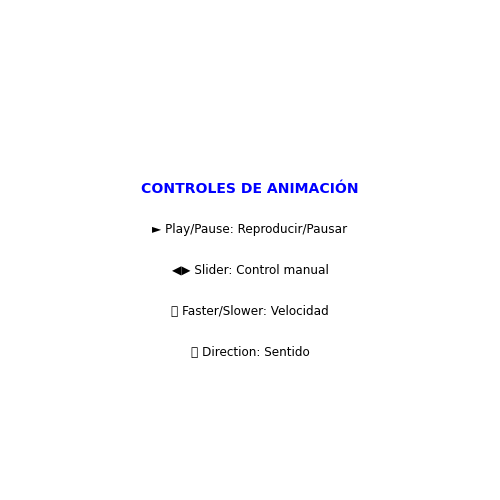
| 
 | -Graphics-

======================================================================

CREANDO ANIMACIÓN COMPARATIVA SIMULTÁNEA

(Las tres órbitas animadas al mismo tiempo)

======================================================================

CREANDO ANIMACIÓN COMPARATIVA SIMULTÁNEA

(Las tres órbitas animadas al mismo tiempo con rangos ajustados)

Rangos individuales calculados:

(a) e=0.5, l=11, M=3/14: 26.4 M

(b) e=0.5, l=7.5, M=3/14: 18. M

(c) e=0.5, l=3, M=3/14: 7.2 M

Animación comparativa con rangos ajustados:

```mathematica
(*Código para graficar y animar órbitas relativistas en Schwarzschild Animaciones detalladas para las tres órbitas (a),(b) y (c)*)ClearAll["Global`*"]

(* =======================================================================*)
(*PARÁMETROS DE LAS ÓRBITAS*)
(* =======================================================================*)

(*Valores de la figura 7a con número de revoluciones para animación*)
paramSets={{"(a) e=0.5, l=11, M=3/14",0.5,11.0,3/14,4},(*4 revoluciones*){"(b) e=0.5, l=7.5, M=3/14",0.5,7.5,3/14,6},(*6 revoluciones*){"(c) e=0.5, l=3, M=3/14",0.5,3.0,3/14,10}    (*10 revoluciones*)};

(* =======================================================================*)
(*FUNCIONES AUXILIARES*)
(* =======================================================================*)

(*Función para calcular μ=M/l*)
CalcMu[M_,l_]:=M/l;

(*Función para calcular A=1-6μ+2μe*)
CalcA[mu_,e_]:=1-6*mu+2*mu*e;

(*Función para calcular k.b2=4μe/A*)
Calck2[mu_,e_,A_]:=If[A!=0,4*mu*e/A,1.0];

(*Función para calcular φ(χ) usando la ecuación (132):φ=2/√A*F(π/2-χ/2,k)*)
PhiFromChi[chi_,A_,k2_]:=Module[{sqrtA,psi},If[A<=0,Return[Indeterminate]];
sqrtA=Sqrt[A];
psi=Pi/2-chi/2;
2*EllipticF[psi,k2]/sqrtA];

(*Función para calcular datos orbitales para animación Devuelve {orbitData,rHorizon,rCritical,phiPerRev,precession}*)
CalcOrbitDataForAnimation[e_,l_,M_,nRevolutions_]:=Module[{mu,A,k2,chiValsOneRev,phiValsOneRev,allChi,allPhi,allR,allX,allY,phiPerRev,precession,orbitData,rHorizon,rCritical},mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
(*Verificar parámetros válidos*)If[A<=0||k2<0,Print["Parámetros inválidos para animación: A = ",A,", k.b2 = ",k2];
Return[{{},0,0,0,0},Module];];
(*Una revolución:χ de π (afelio) a-π (siguiente afelio)*)chiValsOneRev=Range[Pi,-Pi,-2*Pi/199];(*200 puntos por rev*)phiValsOneRev=PhiFromChi[#,A,k2]&/@chiValsOneRev;
(*Ángulo φ por revolución y precesión*)phiPerRev=phiValsOneRev[[-1]]-phiValsOneRev[[1]];
precession=phiPerRev-2*Pi;
(*Generar múltiples revoluciones*)allChi={};
allPhi={};
For[rev=0,rev<nRevolutions,rev++,chiOffset=rev*2*Pi;
phiOffset=rev*phiPerRev;
chiValsAdj=chiValsOneRev-chiOffset;
phiValsAdj=phiValsOneRev-phiValsOneRev[[1]]+phiOffset;
allChi=Join[allChi,chiValsAdj];
allPhi=Join[allPhi,phiValsAdj];];
(*Calcular r=l/(1+e cosχ)*)allR=l/(1+e*Cos[allChi]);
(*Convertir a coordenadas cartesianas*)allX=allR*Cos[allPhi];
allY=allR*Sin[allPhi];
(*Ajustar para que φ empiece en 0*)phiMin=Min[allPhi];
allPhiAdj=allPhi-phiMin;
allX=allR*Cos[allPhiAdj];
allY=allR*Sin[allPhiAdj];
(*Datos de órbita y parámetros importantes*)orbitData=Transpose[{allX,allY}];
rHorizon=2*M;
rCritical=3*M;
{orbitData,rHorizon,rCritical,phiPerRev,precession}];

(* =======================================================================*)
(*FUNCIÓN PARA CREAR UNA ANIMACIÓN INDIVIDUAL*)
(* =======================================================================*)

CreateOrbitAnimation[label_,e_,l_,M_,nRevs_,plotRange_]:=Module[{orbitData,rHorizon,rCritical,phiPerRev,precession,nPoints,animation,mu,A,k2,perihelio,afelio},Print["Creando animación para: ",label];
(*Calcular datos*){orbitData,rHorizon,rCritical,phiPerRev,precession}=CalcOrbitDataForAnimation[e,l,M,nRevs];
If[Length[orbitData]==0,Print["  No se pudo crear animación: parámetros inválidos"];
Return[Graphics[Text["Error en parámetros",{0,0}]]];];
nPoints=Length[orbitData];
(*Parámetros adicionales*)mu=CalcMu[M,l];
A=CalcA[mu,e];
k2=Calck2[mu,e,A];
perihelio=l/(1+e);
afelio=l/(1-e);
Print["  μ = ",NumberForm[mu,4],", k.b2 = ",NumberForm[k2,4]];
Print["  Perihelio: r = ",NumberForm[perihelio,4]];
Print["  Afelio: r = ",NumberForm[afelio,4]];
Print["  Precesión: ",NumberForm[precession*180/Pi,4],"°/rev"];
Print["  Puntos totales: ",nPoints];
(*Crear animación*)animation=Animate[Show[(*1. Fondo:órbita completa en gris claro*)Graphics[{White,Opacity[0.2],Thickness[0.002],Line[orbitData]},PlotRange->plotRange],(*2. Trayectoria recorrida hasta el momento (color progresivo)*)Graphics[{ColorData["Rainbow"][currentFraction],Thickness[0.006],CapForm["Round"],Line[Take[orbitData,Floor[currentFraction*nPoints]]]}],(*3. Punto móvil (partícula)*)Graphics[{EdgeForm[Black],Yellow,Disk[orbitData[[Floor[currentFraction*nPoints]]],0.1],Black,PointSize[0.02],Point[orbitData[[Floor[currentFraction*nPoints]]]]}],(*4. Línea desde el centro al punto actual*)Graphics[{Dashed,Gray,Opacity[0.6],Thickness[0.002],Line[{{0,0},orbitData[[Floor[currentFraction*nPoints]]]}]}],(*5. Elementos fijos del gráfico*)Graphics[{(*Horizonte de eventos*){Black,Opacity[0.15],Disk[{0,0},rHorizon]},(*Órbita circular crítica*){Red,Dashed,Opacity[0.4],Thickness[0.003],Circle[{0,0},rCritical]},(*Centro del agujero negro*){Black,PointSize[0.035],Point[{0,0}]},(*Perihelio y afelio (líneas de referencia)*){Green,Dashed,Opacity[0.3],Thickness[0.001],Circle[{0,0},perihelio]},{Blue,Dashed,Opacity[0.3],Thickness[0.001],Circle[{0,0},afelio]},(*Marcadores de perihelio y afelio*){Green,PointSize[0.02],Point[{afelio,0}]},{Red,PointSize[0.02],Point[{perihelio,0}]}}],(*6. Panel de información dinámica*)Graphics[{(*Fondo semitransparente para el panel*){White,Opacity[0.8],Rectangle[Scaled[{0.02,0.02}],Scaled[{0.38,0.18}]]},(*Texto informativo*)Text[Style[label,14,Bold,Darker[Blue]],Scaled[{0.05,0.16}]],Text[Style[StringForm["Revolución: {`1f`}/{}",currentFraction*nPoints/(nPoints/nRevs),nRevs],12,Darker[Green]],Scaled[{0.05,0.12}]],Text[Style[StringForm["Progreso: {`1f`}%",currentFraction*100],11,Magenta],Scaled[{0.05,0.08}]],Text[Style[StringForm["Precesión: {`4f`}°/rev",precession*180/Pi],10,Darker[Red]],Scaled[{0.05,0.04}]]}],(*7. Indicador de posición angular*)Graphics[{Thin,Gray,Circle[{0,0},0.8*Min[plotRange[[1,2]],plotRange[[2,2]]],{0,2*Pi*currentFraction}],Arrow[{{0,0},0.9*Min[plotRange[[1,2]],plotRange[[2,2]]]*{Cos[2*Pi*currentFraction],Sin[2*Pi*currentFraction]}}]}],(*Configuración del gráfico*)Frame->True,FrameLabel->{Style["x/M",12,Bold],Style["y/M",12,Bold]},FrameStyle->Thickness[0.003],PlotRange->plotRange,AspectRatio->1,ImageSize->500,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted,Opacity[0.2]],Background->Lighter[Gray,0.95]],(*Control de animación*){currentFraction,0,1,0.005},(*Opciones de animación*)AnimationRunning->False,AnimationRepetitions->1,DisplayAllSteps->False,DefaultDuration->30,(*30 segundos para animación completa*)(*Control deslizante personalizado*)ControlPlacement->Bottom,AppearanceElements->{"ProgressSlider","PlayPauseButton","FasterSlowerButtons","DirectionButton"},(*Etiquetas*)LabelStyle->{FontSize->11,FontFamily->"Arial"},TrackedSymbols:>{currentFraction}];
animation];

(* =======================================================================*)
(*CREAR ANIMACIONES PARA LAS TRES ÓRBITAS*)
(* =======================================================================*)

Print[StringRepeat["=",70]];
Print["CREANDO ANIMACIONES DETALLADAS PARA LAS TRES ÓRBITAS"];
Print[StringRepeat["=",70]];

(*Definir rangos de gráfico apropiados para cada órbita*)
plotRanges={{{-25,25},{-25,25}},(*Para (a):órbita más grande*){{-20,20},{-20,20}},(*Para (b):órbita mediana*){{-10,10},{-10,10}}       (*Para (c):órbita más pequeña y cercana*)};

(*Crear las tres animaciones*)
animations=Table[Module[{label,e,l,M,nRevs,plotRange},{label,e,l,M,nRevs}=paramSets[[i]];
plotRange=plotRanges[[i]];
Print["\n",StringRepeat["-",60]];
CreateOrbitAnimation[label,e,l,M,nRevs,plotRange]],{i,1,Length[paramSets]}];

(* =======================================================================*)
(*MOSTRAR ANIMACIONES EN UNA CUADRÍCULA*)
(* =======================================================================*)

Print["\n"<>StringRepeat["=",70]];
Print["MOSTRANDO ANIMACIONES EN CUADRÍCULA"];
Print["(Cada animación tiene controles independientes de reproducción)"];

(*Mostrar las tres animaciones en una cuadrícula*)
Grid[{{animations[[1]],animations[[2]]},{animations[[3]],Graphics[{Text[Style["CONTROLES DE ANIMACIÓN",14,Bold,Blue],{0,0.3}],Text[Style["► Play/Pause: Reproducir/Pausar",12],{0,0.1}],Text[Style["◀▶ Slider: Control manual",12],{0,-0.1}],Text[Style["⏩ Faster/Slower: Velocidad",12],{0,-0.3}],Text[Style["🔄 Direction: Sentido",12],{0,-0.5}]},ImageSize->500,PlotRange->{{-1,1},{-1,1}}]}},Spacings->{30,30},Alignment->Center]

(* =======================================================================*)
(*ANIMACIÓN COMPARATIVA SIMULTÁNEA (OPCIONAL)*)
(* =======================================================================*)

Print["\n"<>StringRepeat["=",70]];
Print["CREANDO ANIMACIÓN COMPARATIVA SIMULTÁNEA"];
Print["(Las tres órbitas animadas al mismo tiempo)"];

(*Preparar datos para animación comparativa*)
orbitDataList=Table[{label,e,l,M,nRevs}=paramSets[[i]];
{orbitData,rHorizon,rCritical,phiPerRev,precession}=CalcOrbitDataForAnimation[e,l,M,3];(*Solo 3 rev para comparación*){label,orbitData,rHorizon,rCritical,precession},{i,1,Length[paramSets]}];


(* =======================================================================*)(*ANIMACIÓN COMPARATIVA SIMULTÁNEA CON RANGOS AJUSTADOS*)(* =======================================================================*)Print["\n"<>StringRepeat["=",70]];
Print["CREANDO ANIMACIÓN COMPARATIVA SIMULTÁNEA"];
Print["(Las tres órbitas animadas al mismo tiempo con rangos ajustados)"];

(*Preparar datos para animación comparativa con rangos individuales*)
orbitDataWithRanges=Table[Module[{label,e,l,M,orbitData,rHorizon,rCritical,phiPerRev,precession,plotRangeIndividual,maxR},{label,e,l,M,nRevs}=paramSets[[i]];
{orbitData,rHorizon,rCritical,phiPerRev,precession}=CalcOrbitDataForAnimation[e,l,M,3];(*3 revoluciones para comparación*)(*Calcular rango individual basado en la órbita*)(*Encontrar el valor máximo absoluto en x e y*)allX=orbitData[[All,1]];
allY=orbitData[[All,2]];
maxX=Max[Abs[allX]];
maxY=Max[Abs[allY]];
maxR=Max[maxX,maxY]*1.2;(*Añadir 20% de margen*)(*Rangos individuales para cada órbita*)plotRangeIndividual={{-maxR,maxR},{-maxR,maxR}};
{label,orbitData,rHorizon,rCritical,plotRangeIndividual}],{i,1,Length[paramSets]}];

(*Mostrar los rangos calculados*)
Print["\nRangos individuales calculados:"];
Do[Print[orbitDataWithRanges[[i,1]],": ",NumberForm[orbitDataWithRanges[[i,5,1,2]],4]," M"];,{i,1,Length[orbitDataWithRanges]}];

(*Crear animación comparativa con rangos ajustados*)
comparativeAnimationAdjusted=Animate[GraphicsGrid[Table[Module[{label,orbitData,rHorizon,rCritical,plotRangeIndiv,nPoints,currentData},{label,orbitData,rHorizon,rCritical,plotRangeIndiv}=orbitDataWithRanges[[i]];
nPoints=Length[orbitData];
currentData=Take[orbitData,Floor[currentTime*nPoints]];
Show[(*Fondo con elementos fijos*)Graphics[{(*Órbita completa en gris*)LightGray,Opacity[0.15],Thickness[0.001],Line[orbitData],(*Horizonte de eventos*)Black,Opacity[0.1],Disk[{0,0},rHorizon],(*Órbita circular crítica*)Red,Opacity[0.2],Dashed,Thickness[0.0015],Circle[{0,0},rCritical],(*Centro*)Black,PointSize[0.015],Point[{0,0}]}],(*Trayectoria recorrida hasta ahora*)Graphics[{(*Color diferente para cada órbita*)Switch[i,1,RGBColor[0.2,0.4,0.8],(*Azul para (a)*)2,RGBColor[0.8,0.4,0.2],(*Naranja para (b)*)3,RGBColor[0.4,0.8,0.2]     (*Verde para (c)*)],Thickness[0.006],CapForm["Round"],Line[currentData]}],(*Punto actual*)Graphics[{EdgeForm[Black],Switch[i,1,RGBColor[0.1,0.3,0.9],(*Azul oscuro*)2,RGBColor[0.9,0.3,0.1],(*Rojo anaranjado*)3,RGBColor[0.1,0.9,0.3]     (*Verde brillante*)],Disk[If[Length[currentData]>0,currentData[[-1]],{0,0}],0.03*plotRangeIndiv[[1,2]]] (*Tamaño proporcional al rango*)}],(*Etiquetas y información*)Graphics[{(*Etiqueta de la órbita*)Text[Style[label,11,Bold,Black],Scaled[{0.05,0.93}]],(*Radio máximo*)Text[Style[StringForm["Rango: ±{`3f`}M",plotRangeIndiv[[1,2]]],8,Gray],Scaled[{0.05,0.05}]],(*Contador de revolución*)Text[Style[StringForm["Rev: {`2f`}",currentTime*nPoints/(nPoints/3)],9,Darker[Gray]],Scaled[{0.85,0.93}]]}],(*Configuración del gráfico*)Frame->True,FrameLabel->If[i==1||i==3,{{"y/M",None},{"x/M",None}},{{None,None},{"x/M",None}}],FrameStyle->If[i==1||i==3,Thickness[0.002],Directive[Thickness[0.002],Opacity[0.5]]],PlotRange->plotRangeIndiv,AspectRatio->1,ImageSize->280,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted,Opacity[0.1]]]],{i,1,3}],Spacings->{5,5}],(*Control de animación*){currentTime,0,1,0.005},(*Opciones de animación*)AnimationRunning->False,AnimationRepetitions->1,DefaultDuration->25,ControlPlacement->Bottom,AppearanceElements->{"ProgressSlider","PlayPauseButton","FasterSlowerButtons"},(*Etiqueta del control*)Paneled->True,FrameLabel->{{None,None},{None,Style["Animación Comparativa - Tiempo Normalizado",12,Bold]}}];

(*Mostrar animación comparativa*)
Print["\nAnimación comparativa con rangos ajustados:"];
comparativeAnimationAdjusted
```